```mathematica
l=10; 
fmtoMeV=197; (* conversion factor between fermi and MeV *)
p[n1_,n2_,n3_]:=(2*π)/l*{n1,n2,n3}*fmtoMeV;
```

```mathematica
N[p[1,0,0]]
```

{123.779,0.,0.}

```mathematica
mpi=140; (* Mass of the pion in MeV *)
psquared[n_]:=(4*π^2)/l^2*n^2
energy[n1_,n2_,n3_]:=√(mpi^2+Norm[p[n1,n2,n3]]^2); (* Lab energy of a single pion in cube of size l *)
Nmag[n1_,n2_,n3_]:=Norm[{n1,n2,n3}]^2;
```

```mathematica
Data={};
For[i=0,i<5,i++,
For[j=0,j<5,j++,
For[k=0,k<5,k++,
e=energy[i,j,k];
n=Nmag[i,j,k];
If[MemberQ[Data,{n,e}],Continue[],AppendTo[Data,{n,e}]];
]
]
]
```

```mathematica
Data;
```

```mathematica
Clear[Data]
```

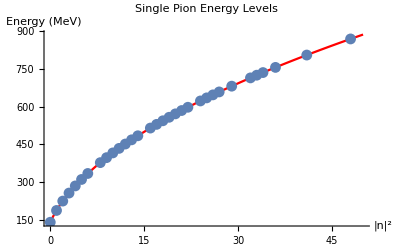

```mathematica
lp=ListPlot[Data,AxesLabel->{"|n|^2","Energy (MeV)"},PlotLabel->"Single Pion Energy Levels"];
p11=Plot[√(mpi^2+((2*π)/l)^2*x*fmtoMeV^2),{x,0,50},PlotStyle->Red,AxesLabel->{"|n|^2","Energy (MeV)"},PlotLabel->"Single Pion Energy Levels"];
Show[p11,lp]
```

```mathematica
Data;
```

```mathematica
pl[n1_,n2_,n3_,L_]:=(2*π)/L*{n1,n2,n3}*fmtoMeV; (* momentum of a single particle in a cube of size L in MeV *)
energyl[n1_,n2_,n3_,L_]:=√(mpi^2+Norm[pl[n1,n2,n3,L]]^2); (* Lab energy of a single pion in cube of size l *)
```

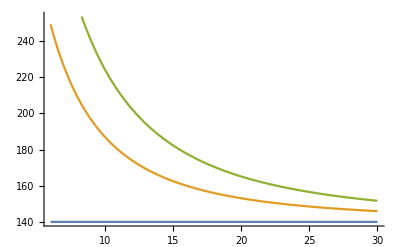

```mathematica
Plot[{energyl[0,0,0,x],energyl[1,0,0,x],energyl[1,1,0,x]},{x,6,30}]
```

```mathematica
d[i1_,j1_,k1_,i2_,j2_,k2_]:={i1+i2,j1+j2,k1+k2};
energydl[n1_,n2_,n3_,d1_,d2_,d3_,L_]:=energyl[n1,n2,n3,L]+energyl[d1-n1,d2-n2,d3-n3,L]; (* Total energy in lab frame *)
ptot[d1_,d2_,d3_,L_]:=(2*π)/L*{d1,d2,d3}*fmtoMeV; (* total momentum in lab frame *)
ecmld[n1_,n2_,n3_,d1_,d2_,d3_,L_]:=√((energydl[n1,n2,n3,d1,d2,d3,L])^2-(Norm[ptot[d1,d2,d3,L]])^2); (* center of mass energy for two pions in a cube of size L *)
ecmld0[nval_,L_]:=2*√(mpi^2+((2*π)/L)^2*nval*fmtoMeV^2);
```

```mathematica
Manipulate[N[{ecmld[n1,n2,n3,d1,d2,d3,6],ecmld0[Norm[{n1,n2,n3}]^2,6]}],{n1,0,5,1},{n2,0,5,1},{n3,0,5,1},{d1,0,5,1},{d2,0,5,1},{d3,0,5,1}]
```

```mathematica
nvalues={};
Plots0={};
For[nval=0,nval≤10,nval++,
p0=Plot[ecmld0[nval,L],{L,6,30},PlotRange->{100,1500},PlotLabel->"d=0 Energy Spectrum",AxesLabel->{"L (fm)","Energy (MeV)"}];
AppendTo[Plots0,p0];
]
```

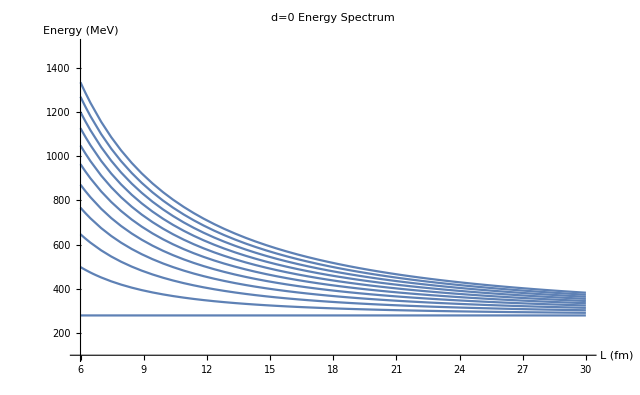

```mathematica
Show[Plots0]
```

{1,2,5,3,6,9,4,8,12,10,13,11,14,17}

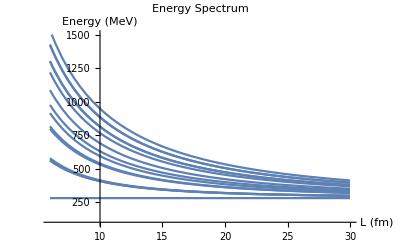

```mathematica
Clear[dPlots,nvalues]
dPlots={}; (* List to hold plots *)
nvalues={}; (* list to hold plotted values of |n|^2 *)
dValue=2; (* total boosts value to calculate plots for *)
AppendTo[dPlots,Plot[ecmld[0,0,0,0,0,0,L],{L,6,30},PlotRange->{100,1500},PlotLabel->"Energy Spectrum",AxesLabel->{"L (fm)","Energy (MeV)"}]]; (* Plot threshold energy *)
(* Loops to run over possible boosts and momentum values *)
For[d1=0,d1<3,d1++,
For[d2=0,d2<3,d2++,
For[d3=0,d3<3,d3++,
dmagsq=(Norm[{d1,d2,d3}])^2;
If[dmagsq==dValue,
For[n1=1,n1≤3,n1++,
For[n2=0,n2≤2,n2++,
For[n3=0,n3≤2,n3++,
nmagsq=(Norm[{n1,n2,n3}])^2;
If[MemberQ[nvalues,nmagsq],,
pd=Plot[ecmld[n1,n2,n3,d1,d2,d3,L],{L,6,30},PlotRange->{100,1500},PlotLabel->"Energy Spectrum",AxesLabel->{"L (fm)","Energy (MeV)"}];
AppendTo[dPlots,pd];
AppendTo[nvalues,nmagsq];
]
]
]
]
,]
]
]
]
nvalues (* Show plotted values of |n|^2 *)
Show[dPlots](* Show Plots *)
```

```mathematica
nvalue=10;
For[n3=0,n3<4,n3++,
For[n2=0,n2<4,n2++,
For[n1=0,n1<4,n1++,
If[(Norm[{n1,n2,n3}])^2==nvalue,
Print["{",n1,",",n2,",",n3,"}"]
,]
]
]
]
```

{3,1,0}

{1,3,0}

{3,0,1}

{0,3,1}

{1,0,3}

{0,1,3}